# Lamb-Dicke parameter

P. Huft

The Lamb-Dicke parameter is defined as the square root of the ratio of the photon recoil energy to the energy spacing between number states of a harmonic potential.

## Neutral atoms in a red FORT

```mathematica
kB=1.38*10^-23;
TFORT=1*^-3;
U0=kB TFORT;
m=1.4192261×10^-25(*87Rb*)
w0=0.75*10^-6;
λ=0.78*10^-6;
k=(2π)/λ;
ℏ=1.05*10^-34;
ωrecoil=(ℏ k^2)/(2m);
zR=(π w0^2)/λ;
ωr =2/w0 √(U0/m);
ωz =1/zR √(U0/m);
"ωr/2π"
ωr/(2π)
"ωz/2π"
ωz/(2π)
"ωrecoil/2π"
ωrecoil/(2π)
"ηr"
ηr=√(ωrecoil/ωr)
"ηz"
ηz=√(ωrecoil/ωz)
```

1.41923×10^-25

ωr/2π

132343.

ωz/2π

21905.6

ωrecoil/2π

3820.31

ηr

0.169902

ηz

0.41761

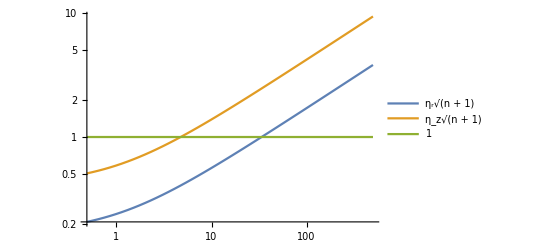

```mathematica
LogLogPlot[{ηr √(n+1),ηz √(n+1),1},{n,0,500},PlotLegends->{"η_r√(n + 1)","η_z√(n + 1)","1"}]
```

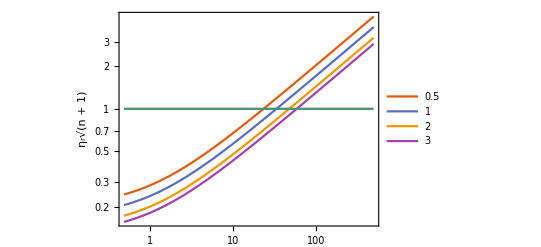

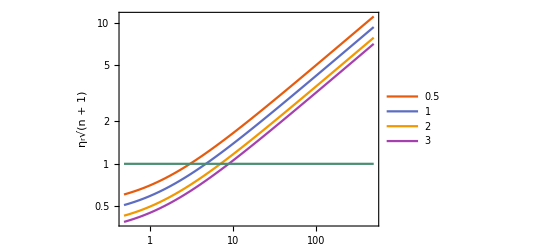

```mathematica
TmKList={0.5,1,2,3};
LogLogPlot[Evaluate[Join@{Table[√(ωrecoil/(2/w0 √((kB TmK*10^-3)/m)))√(n+1),{TmK,TmKList}],{1}}],{n,0,500},PlotLegends->TmKList,PlotTheme->"Scientific",FrameLabel->{"","η_r√(n + 1)"},LabelStyle->Directive[Black, FontSize->12]]
LogLogPlot[Evaluate[Join@{Table[√(ωrecoil/(1/zR √((kB TmK*10^-3)/m)))√(n+1),{TmK,TmKList}],{1}}],{n,0,500},PlotLegends->TmKList,PlotTheme->"Scientific",FrameLabel->{"","η_r√(n + 1)"},LabelStyle->Directive[Black, FontSize->12]]
```

What is the mean vibrational quantum number for atoms of a given temperature? The plot below shows that our atoms should be in the Lamb-Dicke regime in both radial and axial directions as long as the temperature is below about 35 μK, which gives mean n < 5 for our 1 mK trap.

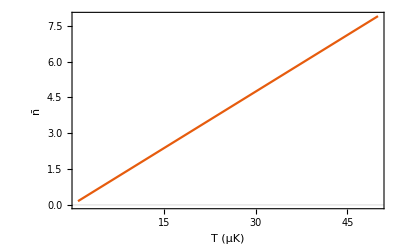

```mathematica
Plot[(kB*10^-6 TμK)/(ℏ ωr),{TμK,1,50 },PlotTheme->"Scientific",FrameLabel->{"T (μK)","n̄"},LabelStyle->Directive[Black, FontSize->12]]
```